## Initialization

### Import dependencies

```mathematica
(* Run bubble-4a-murphree.nb before. *)
```

```mathematica
packageDirectory=FileNameJoin@{NotebookDirectory[],"mathematica_packages\\"}
outputDirectory=FileNameJoin@{NotebookDirectory[],"output\\"}
```

C:\Users\josep\forschung\modeling\bubble_bec\mathematica_packages

C:\Users\josep\forschung\modeling\bubble_bec\output

```mathematica
If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]
```

```mathematica
Get["MovingTrap-murphree.m"]
Get["FitCurveHacked-mean-murphree.m"]
Get["SMThreeTraps.m"]
Get["SMThreeChipModel.m"]
```

Syntax::sntx: Invalid syntax in or before 
    "{{eVec1,\!\(\*SubscriptBox[\(ω\),
        \(1\)]\)},{eVec2,\!\(\*SubscriptBox[\(ω\),
        \(2\)]\)},{eVec3,\!\(\*SubscriptBox[\(ω\), \(3\)]\)}}."*);
                                                                                   
                                                                                   
         ^
      " (line 73 of "MovingTrap-murphree.m").

The following variables used by ExpansionPlotHacked are protected by this package: {axis, trap, usemodel, frequency, trapposition, gridlines, size, meanfrequency, meanmodel}

### Define initial and final trap parameters

```mathematica
trapzero=convertCALTableToTrapParameters@tableZLHb
trapone=convertCALTableToTrapParameters@tableZHbB3
```

{0.,0,0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

{0.,0,0.,2.425,2.6,-1.95,3.55435,-3.11335}

```mathematica
testName="name";
Which[
SameQ[testName,"name"],Print["yes!"]
];
```

yes!

### Define target ramp analytic function

```mathematica
(*cass[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2 t^(1/4) -1)]/Tanh[5];
cassShort[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2(t/2)^(1/4) -1)]/Tanh[5];*)
```

```mathematica
(*omegaPlot=Plot[cassShort[800,50,t]^2,{t,0,1},PlotRange->All];
dOmegaPlot=Plot[Evaluate[(1/0.5)*Abs@D[cassShort[800,50,t],t]],{t,0,1},PlotRange->All,PlotStyle->{"Red"}];
Show[omegaPlot,dOmegaPlot,PlotRange->{{0,1},{0,6400}}]*)
```

```mathematica
(*periodT=0.250 (* [s] *);
omegaI=800 (* [Hz] *);
omegaF=20 (* [Hz] *);
Plot[{cassShort[omegaI,omegaF,t]^2,Evaluate[(1/periodT)*Abs@D[cassShort[omegaI,omegaF,t],t]]},
{t,0,1},PlotRange->All,PlotStyle->{"Blue","Red"}]*)
```

```mathematica
(*Plot[{cassShort[omegaI,omegaF,t]^2,Evaluate[(1/periodT)*Abs@D[cassShort[omegaI,omegaF,t],t]]},
{t,0,1},PlotRange->{{0,1},{0,1*10^4}},PlotStyle->{"Blue","Red"}]*)
```

```mathematica
(*
*)
```

```mathematica
(*num=20;
times={0,0.0085,0.017,0.024,0.032,0.04,0.047,0.056,0.068,0.095,0.127,0.142,0.157,0.172,0.189,0.208,0.233,0.267,0.33,0.4,1};
Length@times
Plot[Evaluate[D[cassShort[1,0,t],{t,1}]],{t,0,1},GridLines->{times,Table[-k*max/(num/2),{k,1,num/2}]}]*)
```

```mathematica
(*Length@Differences@times*)
```

```mathematica
(*Plot[cassShort[1,0,t],{t,0,1},GridLines->{times,{}},PlotRange->Full]*)
```

```mathematica
(*max=MaxValue[{Abs@Evaluate[D[cassShort[1,0,t],{t,1}]],t>0.01},t]*)
```

```mathematica
(*dCassShort[t_]=Evaluate[D[cassShort[1,0,t],{t,1}]];*)
```

```mathematica
(*(*InverseFunction@dCassShort*)*)
```

```mathematica
(*(*cassShortInv=InverseFunction@dCassShort*)*)
```

```mathematica
(*(*cassShortInv[-max]*)*)
```

```mathematica
(*Plot[Evaluate[D[cassShort[1,0,t],{t,2}]],{t,0,1},PlotRange->{{0,1},{-80,40}}]*)
```

```mathematica
(*corgierSimp[t_]:=Module[{tau=2*Pi*t},
(1/(12*Pi))*(6*tau-8*Sin[tau]+Sin[2*tau])];*)
```

```mathematica
(*Plot[1-corgierSimp[t],{t,0,1}]*)
```

```mathematica
(*Plot[Evaluate@D[1-corgierSimp[t],t],{t,0,1}]*)
```

```mathematica
(*InverseFunction[corgierSimp][8/3]*)
```

```mathematica
(*Plot[Evaluate@D[1-corgierSimp[t],{t,2}],{t,0,1}]*)
```

```mathematica
(*ArcCos[-1-2*Sqrt[2*6/10]]/(2*Pi)//N*)
```

```mathematica
(*trapAnalytic[trap1_,trap2_,t_]:=trap1+(trap2-trap1)*(1-cassShort[1,0,t]);
zeroCrossing[trap1_,trap2_]:=(1/8)*((1/5)*ArcTanh[2*Tanh[5]*((1/2)-trap2[[6]]/(trap2[[6]]-trap1[[6]]))]+1)^4;*)
```

```mathematica
(*Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All]
tauZero=zeroCrossing[trapzero,trapone]
period=500*10^(-3);
deltaTau=10*^-3/period;
newTaus={tauZero-deltaTau,tauZero,tauZero+deltaTau};
Print["tZero = "<>ToString[tauZero*period]]*)
```

```mathematica
(*Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,rampin1sguess⟦1⟧}]*)
```

```mathematica
(*Show[{
Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All],
ListPlot[Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,Accumulate@rampin1sguess⟦1⟧}]]
}]*)
```

### Define ramp ansatz

#### Trap 1 Short

The first component of this object defines how to distribute the duration of each linear ramp in the ramp sequence. The durations are expressed as a fraction of the ramp sequence’s total duration, and so must sum to 1.

The second component of this object nominally is a guess at the fractional change of the ramp sequence for that linear ramp, but is not used by any of the fitting components and is considered vestigial.

```mathematica
rampin1sguess={2*{0.01,0.01,0.01,0.01,0.01,0.01,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.025,0.04,0.07,0.08,0.09},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}};
```

```mathematica
rampin1sguess={
{0.02720,.01420,.01160,.01020,.00960,.0090,.0090,.00880,.00880,.00920,.00460,.00480,.00480,.0050,.0050,.00540,.00560,.00580,.0060,.00640,.00660,.00720,.00760,.00820,.00880,.00960,.01060,.01160,.0130,.01480,.01660,.01960,.02280,.02780,.03460,.04460,.06060,.08920,.14960,.2656},
{0.04,0.04,0.04,0.04,0.04,0.04,0.04125,0.04,0.04,0.04,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02125,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.0175}
}
```

{{0.0272,0.0142,0.0116,0.0102,0.0096,0.009,0.009,0.0088,0.0088,0.0092,0.0046,0.0048,0.0048,0.005,0.005,0.0054,0.0056,0.0058,0.006,0.0064,0.0066,0.0072,0.0076,0.0082,0.0088,0.0096,0.0106,0.0116,0.013,0.0148,0.0166,0.0196,0.0228,0.0278,0.0346,0.0446,0.0606,0.0892,0.1496,0.2656},{0.04,0.04,0.04,0.04,0.04,0.04,0.04125,0.04,0.04,0.04,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02125,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.0175}}

Check that both components sum to 1.

```mathematica
Total[rampin1sguess⟦1⟧]
Total[rampin1sguess⟦2⟧]
```

1.

1.

Check the specified number of constituent linear ramps.

```mathematica
numberOfSequencePoints=Length@rampin1sguess⟦1⟧
```

40

## Calculate ramp

The following took 40 minutes to complete. (29 Sept. 2020)

```mathematica
(* 
If FitCurveHacked runs in less than a second and has multiple errors citing GeometricMean, go back and make sure bubble-4a.nb was run before this notebook. MovingTrap-murphree.m calls ChipTrapFrequencies, which is defined in that notebook.
*)
```

```mathematica
(rampin1s=FitCurveHacked[trapzero,trapone,rampin1sguess,numberOfSequencePoints,-3.5,-5,"SackettTanhLong"])//Timing
```

{0.04,37.6163,0.131026,414.341,451.957,1.,0}

{0.52,-223.953,0.131026,414.341,190.388,1.,0.04}

{0.28,-96.2101,0.131026,414.341,318.131,0.52,0.04}

{0.16,-29.1641,0.131026,414.341,385.177,0.28,0.04}

{0.1,4.34269,0.131026,414.341,418.684,0.16,0.04}

{0.13,-12.3908,0.131026,414.341,401.95,0.16,0.1}

{0.115,-4.01787,0.131026,414.341,410.323,0.13,0.1}

{0.1075,0.164109,0.131026,414.341,414.505,0.115,0.1}

{0.11125,-1.92648,0.131026,414.341,412.415,0.115,0.1075}

{0.10938,-0.883867,0.131026,414.341,413.457,0.11125,0.1075}

{0.10844,-0.359853,0.131026,414.341,413.981,0.10938,0.1075}

Completed point 1 of 39 in 62.375 s (Total time: 1.03958 min).

{0.0382572,41.723,0.111046,351.158,392.881,0.89203,0}

{0.46514,-186.389,0.111046,351.158,164.769,0.89203,0.0382572}

{0.2517,-76.9009,0.111046,351.158,274.257,0.46514,0.0382572}

{0.14498,-17.9676,0.111046,351.158,333.19,0.2517,0.0382572}

{0.09162,11.8583,0.111046,351.158,363.016,0.14498,0.0382572}

{0.1183,-3.06796,0.111046,351.158,348.09,0.14498,0.09162}

{0.10496,4.39298,0.111046,351.158,355.551,0.1183,0.09162}

{0.11163,0.661822,0.111046,351.158,351.82,0.1183,0.10496}

{0.11496,-1.20046,0.111046,351.158,349.958,0.1183,0.11163}

{0.1133,-0.272162,0.111046,351.158,350.886,0.11496,0.11163}

{0.11246,0.197615,0.111046,351.158,351.356,0.1133,0.11163}

Completed point 2 of 39 in 63.8125 s (Total time: 2.10313 min).

{0.0362934,36.8745,0.0929639,293.978,330.852,0.77915,0}

{0.40772,-154.333,0.0929639,293.978,139.645,0.77915,0.0362934}

{0.22201,-64.2287,0.0929639,293.978,229.749,0.40772,0.0362934}

{0.12915,-14.4467,0.0929639,293.978,279.531,0.22201,0.0362934}

{0.08272,11.0856,0.0929639,293.978,305.063,0.12915,0.0362934}

{0.10594,-1.72299,0.0929639,293.978,292.255,0.12915,0.08272}

{0.09433,4.67233,0.0929639,293.978,298.65,0.10594,0.08272}

{0.10014,1.46956,0.0929639,293.978,295.447,0.10594,0.09433}

{0.10304,-0.12732,0.0929639,293.978,293.85,0.10594,0.10014}

{0.10159,0.67097,0.0929639,293.978,294.649,0.10304,0.10014}

{0.10232,0.269035,0.0929639,293.978,294.247,0.10304,0.10159}

Completed point 3 of 39 in 65.4375 s (Total time: 3.19375 min).

{0.0344992,29.0795,0.0778146,246.071,275.151,0.67647,0}

{0.35548,-127.591,0.0778146,246.071,118.481,0.67647,0.0344992}

{0.19499,-54.9505,0.0778146,246.071,191.121,0.35548,0.0344992}

{0.11474,-13.9145,0.0778146,246.071,232.157,0.19499,0.0344992}

{0.07462,7.38672,0.0778146,246.071,253.458,0.11474,0.0344992}

{0.09468,-3.31869,0.0778146,246.071,242.753,0.11474,0.07462}

{0.08465,2.02107,0.0778146,246.071,248.092,0.09468,0.07462}

{0.08966,-0.649475,0.0778146,246.071,245.422,0.09468,0.08465}

{0.08716,0.682316,0.0778146,246.071,246.754,0.08966,0.08465}

Completed point 4 of 39 in 51.7344 s (Total time: 4.05599 min).

{0.0330017,22.5991,0.0651619,206.06,228.659,0.58806,0}

{0.31053,-104.396,0.0651619,206.06,101.664,0.58806,0.0330017}

{0.17177,-46.2303,0.0651619,206.06,159.83,0.31053,0.0330017}

{0.10239,-12.8588,0.0651619,206.06,193.201,0.17177,0.0330017}

{0.0677,4.64464,0.0651619,206.06,210.705,0.10239,0.0330017}

{0.08504,-4.16485,0.0651619,206.06,201.895,0.10239,0.0677}

{0.07637,0.225395,0.0651619,206.06,206.285,0.08504,0.0677}

{0.0807,-1.97089,0.0651619,206.06,204.089,0.08504,0.07637}

{0.07854,-0.876197,0.0651619,206.06,205.184,0.0807,0.07637}

{0.07746,-0.328168,0.0651619,206.06,205.732,0.07854,0.07637}

Completed point 5 of 39 in 59.5625 s (Total time: 5.0487 min).

{0.0317469,16.0803,0.0550259,174.007,190.088,0.51114,0}

{0.27144,-85.8749,0.0550259,174.007,88.1324,0.51114,0.0317469}

{0.15159,-39.4997,0.0550259,174.007,134.508,0.27144,0.0317469}

{0.09167,-12.7021,0.0550259,174.007,161.305,0.15159,0.0317469}

{0.06171,1.46485,0.0550259,174.007,175.472,0.09167,0.0317469}

{0.07669,-5.67759,0.0550259,174.007,168.33,0.09167,0.06171}

{0.0692,-2.12072,0.0550259,174.007,171.887,0.07669,0.06171}

{0.06546,-0.333867,0.0550259,174.007,173.673,0.0692,0.06171}

{0.06358,0.567011,0.0550259,174.007,174.574,0.06546,0.06171}

{0.06452,0.11635,0.0550259,174.007,174.124,0.06546,0.06358}

{0.06499,-0.108814,0.0550259,174.007,173.898,0.06546,0.06452}

Completed point 6 of 39 in 66.7031 s (Total time: 6.16042 min).

{0.0320259,11.7047,0.0465581,147.23,158.934,0.44638,0}

{0.2392,-69.9188,0.0465581,147.23,77.3108,0.44638,0.0320259}

{0.13561,-32.8246,0.0465581,147.23,114.405,0.2392,0.0320259}

{0.08382,-11.429,0.0465581,147.23,135.801,0.13561,0.0320259}

{0.05792,-0.0646529,0.0465581,147.23,147.165,0.08382,0.0320259}

{0.04497,5.77228,0.0465581,147.23,153.002,0.05792,0.0320259}

{0.05144,2.84355,0.0465581,147.23,150.073,0.05792,0.04497}

{0.05468,1.38629,0.0465581,147.23,148.616,0.05792,0.05144}

{0.0563,0.660023,0.0465581,147.23,147.89,0.05792,0.05468}

{0.05711,0.297486,0.0465581,147.23,147.527,0.05792,0.0563}

{0.05752,0.114131,0.0465581,147.23,147.344,0.05792,0.05711}

Completed point 7 of 39 in 64.375 s (Total time: 7.23333 min).

{0.0299973,8.44699,0.0397437,125.681,134.128,0.38866,0}

{0.20933,-57.0669,0.0397437,125.681,68.6137,0.38866,0.0299973}

{0.11966,-27.1575,0.0397437,125.681,98.5231,0.20933,0.0299973}

{0.07483,-10.063,0.0397437,125.681,115.618,0.11966,0.0299973}

{0.05241,-0.97838,0.0397437,125.681,124.702,0.07483,0.0299973}

{0.0412,3.69372,0.0397437,125.681,129.374,0.05241,0.0299973}

{0.0468,1.3491,0.0397437,125.681,127.03,0.05241,0.0412}

{0.0496,0.184754,0.0397437,125.681,125.865,0.05241,0.0468}

{0.051,-0.395418,0.0397437,125.681,125.285,0.05241,0.0496}

{0.0503,-0.105499,0.0397437,125.681,125.575,0.051,0.0496}

Completed point 8 of 39 in 59.8438 s (Total time: 8.23073 min).

{0.0293738,5.76362,0.0341765,108.076,113.839,0.33871,0}

{0.18404,-46.7479,0.0341765,108.076,61.3276,0.33871,0.0293738}

{0.10671,-22.5722,0.0341765,108.076,85.5034,0.18404,0.0293738}

{0.06804,-8.94161,0.0341765,108.076,99.134,0.10671,0.0293738}

{0.04871,-1.72462,0.0341765,108.076,106.351,0.06804,0.0293738}

{0.03904,1.98677,0.0341765,108.076,110.062,0.04871,0.0293738}

{0.04388,0.120761,0.0341765,108.076,108.196,0.04871,0.03904}

{0.0463,-0.805938,0.0341765,108.076,107.27,0.04871,0.04388}

{0.04509,-0.343115,0.0341765,108.076,107.732,0.0463,0.04388}

{0.04448,-0.109391,0.0341765,108.076,107.966,0.04509,0.04388}

Completed point 9 of 39 in 58.3125 s (Total time: 9.2026 min).

{0.0288961,4.12107,0.0294651,93.1769,97.298,0.29453,0}

{0.16171,-37.9975,0.0294651,93.1769,55.1794,0.29453,0.0288961}

{0.0953,-18.4011,0.0294651,93.1769,74.7758,0.16171,0.0288961}

{0.0621,-7.52782,0.0294651,93.1769,85.6491,0.0953,0.0288961}

{0.0455,-1.80259,0.0294651,93.1769,91.3743,0.0621,0.0288961}

{0.0372,1.13377,0.0294651,93.1769,94.3107,0.0455,0.0288961}

{0.04135,-0.340589,0.0294651,93.1769,92.8363,0.0455,0.0372}

{0.03928,0.393267,0.0294651,93.1769,93.5702,0.04135,0.0372}

Completed point 10 of 39 in 49.2031 s (Total time: 10.0227 min).

{0.00851533,3.34976,0.0274671,86.8585,90.2083,0.25421,0}

{0.13136,-34.3922,0.0274671,86.8585,52.4663,0.25421,0.00851533}

{0.06994,-16.7392,0.0274671,86.8585,70.1193,0.13136,0.00851533}

{0.03923,-7.01884,0.0274671,86.8585,79.8397,0.06994,0.00851533}

{0.02387,-1.9164,0.0274671,86.8585,84.9421,0.03923,0.00851533}

{0.01619,0.696717,0.0274671,86.8585,87.5552,0.02387,0.00851533}

{0.02003,-0.615044,0.0274671,86.8585,86.2435,0.02387,0.01619}

{0.01811,0.0395335,0.0274671,86.8585,86.898,0.02003,0.01619}

{0.01907,-0.288081,0.0274671,86.8585,86.5704,0.02003,0.01811}

{0.01859,-0.124355,0.0274671,86.8585,86.7341,0.01907,0.01811}

{0.01835,-0.0424311,0.0274671,86.8585,86.8161,0.01859,0.01811}

Completed point 11 of 39 in 62.5625 s (Total time: 11.0654 min).

{0.00818034,3.12939,0.025601,80.9575,84.0869,0.23598,0}

{0.12208,-30.8786,0.025601,80.9575,50.0789,0.23598,0.00818034}

{0.06513,-14.8921,0.025601,80.9575,66.0654,0.12208,0.00818034}

{0.03666,-6.15322,0.025601,80.9575,74.8043,0.06513,0.00818034}

{0.02242,-1.5813,0.025601,80.9575,79.3762,0.03666,0.00818034}

{0.0153,0.756545,0.025601,80.9575,81.714,0.02242,0.00818034}

{0.01886,-0.416742,0.025601,80.9575,80.5407,0.02242,0.0153}

{0.01708,0.168807,0.025601,80.9575,81.1263,0.01886,0.0153}

{0.01797,-0.124241,0.025601,80.9575,80.8333,0.01886,0.01708}

Completed point 12 of 39 in 51.6719 s (Total time: 11.9266 min).

{0.00784679,2.73297,0.023934,75.6858,78.4188,0.21846,0}

{0.11315,-27.8558,0.023934,75.6858,47.8301,0.21846,0.00784679}

{0.0605,-13.4078,0.023934,75.6858,62.278,0.11315,0.00784679}

{0.03417,-5.56042,0.023934,75.6858,70.1254,0.0605,0.00784679}

{0.02101,-1.47182,0.023934,75.6858,74.214,0.03417,0.00784679}

{0.01443,0.61547,0.023934,75.6858,76.3013,0.02101,0.00784679}

{0.01772,-0.431799,0.023934,75.6858,75.254,0.02101,0.01443}

{0.01608,0.0893357,0.023934,75.6858,75.7752,0.01772,0.01443}

{0.0169,-0.171457,0.023934,75.6858,75.5144,0.01772,0.01608}

{0.01649,-0.041117,0.023934,75.6858,75.6447,0.0169,0.01608}

{0.01628,0.0256861,0.023934,75.6858,75.7115,0.01649,0.01608}

Completed point 13 of 39 in 60.0938 s (Total time: 12.9281 min).

{0.00753037,2.51242,0.022385,70.7876,73.3,0.20207,0}

{0.1048,-25.0246,0.022385,70.7876,45.763,0.20207,0.00753037}

{0.05617,-11.9615,0.022385,70.7876,58.8261,0.1048,0.00753037}

{0.03185,-4.90969,0.022385,70.7876,65.8779,0.05617,0.00753037}

{0.01969,-1.24619,0.022385,70.7876,69.5414,0.03185,0.00753037}

{0.01361,0.621109,0.022385,70.7876,71.4087,0.01969,0.00753037}

{0.01665,-0.315536,0.022385,70.7876,70.4721,0.01969,0.01361}

{0.01513,0.152035,0.022385,70.7876,70.9396,0.01665,0.01361}

{0.01589,-0.0819379,0.022385,70.7876,70.7057,0.01665,0.01513}

{0.01551,0.0350017,0.022385,70.7876,70.8226,0.01589,0.01513}

{0.0157,-0.0234798,0.022385,70.7876,70.7641,0.01589,0.01551}

Completed point 14 of 39 in 60.9219 s (Total time: 13.9435 min).

{0.00722,2.16519,0.0210052,66.4242,68.5894,0.18647,0}

{0.09684,-22.5914,0.0210052,66.4242,43.8329,0.18647,0.00722}

{0.05203,-10.7985,0.0210052,66.4242,55.6257,0.09684,0.00722}

{0.02962,-4.4676,0.0210052,66.4242,61.9566,0.05203,0.00722}

{0.01842,-1.19028,0.0210052,66.4242,65.2339,0.02962,0.00722}

{0.01282,0.477557,0.0210052,66.4242,66.9018,0.01842,0.00722}

{0.01562,-0.358821,0.0210052,66.4242,66.0654,0.01842,0.01282}

{0.01422,0.0587516,0.0210052,66.4242,66.483,0.01562,0.01282}

{0.01492,-0.150188,0.0210052,66.4242,66.274,0.01562,0.01422}

{0.01457,-0.0457569,0.0210052,66.4242,66.3785,0.01492,0.01422}

Completed point 15 of 39 in 56.375 s (Total time: 14.8831 min).

{0.0069328,2.13418,0.019682,62.24,64.3742,0.17207,0}

{0.0895,-20.1606,0.019682,62.24,42.0794,0.17207,0.0069328}

{0.04822,-9.50412,0.019682,62.24,52.7359,0.0895,0.0069328}

{0.02758,-3.81185,0.019682,62.24,58.4281,0.04822,0.0069328}

{0.01726,-0.872057,0.019682,62.24,61.3679,0.02758,0.0069328}

{0.0121,0.621865,0.019682,62.24,62.8619,0.01726,0.0069328}

{0.01468,-0.127118,0.019682,62.24,62.1129,0.01726,0.0121}

{0.01339,0.246866,0.019682,62.24,62.4869,0.01468,0.0121}

{0.01404,0.0582981,0.019682,62.24,62.2983,0.01468,0.01339}

{0.01436,-0.0344411,0.019682,62.24,62.2055,0.01468,0.01404}

Completed point 16 of 39 in 59.5625 s (Total time: 15.8758 min).

{0.00663,1.93609,0.0184701,58.4077,60.3438,0.15787,0}

{0.08225,-18.0254,0.0184701,58.4077,40.3822,0.15787,0.00663}

{0.04444,-8.45291,0.0184701,58.4077,49.9548,0.08225,0.00663}

{0.02553,-3.36016,0.0184701,58.4077,55.0475,0.04444,0.00663}

{0.01608,-0.738239,0.0184701,58.4077,57.6694,0.02553,0.00663}

{0.01135,0.593727,0.0184701,58.4077,59.0014,0.01608,0.00663}

{0.01372,-0.075313,0.0184701,58.4077,58.3324,0.01608,0.01135}

{0.01254,0.25738,0.0184701,58.4077,58.6651,0.01372,0.01135}

{0.01313,0.090931,0.0184701,58.4077,58.4986,0.01372,0.01254}

Completed point 17 of 39 in 52.4063 s (Total time: 16.7492 min).

{0.00633478,1.73211,0.0173646,54.9116,56.6437,0.14445,0}

{0.07539,-16.1039,0.0173646,54.9116,38.8077,0.14445,0.00633478}

{0.04086,-7.52682,0.0173646,54.9116,47.3848,0.07539,0.00633478}

{0.0236,-2.98272,0.0173646,54.9116,51.9289,0.04086,0.00633478}

{0.01497,-0.647398,0.0173646,54.9116,54.2642,0.0236,0.00633478}

{0.01065,0.537627,0.0173646,54.9116,55.4492,0.01497,0.00633478}

{0.01281,-0.0562281,0.0173646,54.9116,54.8554,0.01497,0.01065}

{0.01173,0.240363,0.0173646,54.9116,55.1519,0.01281,0.01065}

{0.01227,0.0919837,0.0173646,54.9116,55.0036,0.01281,0.01173}

{0.01254,0.0178568,0.0173646,54.9116,54.9294,0.01281,0.01227}

{0.01268,-0.0205628,0.0173646,54.9116,54.891,0.01281,0.01254}

Completed point 18 of 39 in 62.3906 s (Total time: 17.7891 min).

{0.00604955,1.52693,0.0163596,51.7336,53.2606,0.13184,0}

{0.06894,-14.3792,0.0163596,51.7336,37.3545,0.13184,0.00604955}

{0.03749,-6.71231,0.0163596,51.7336,45.0213,0.06894,0.00604955}

{0.02177,-2.66258,0.0163596,51.7336,49.0711,0.03749,0.00604955}

{0.01391,-0.585366,0.0163596,51.7336,51.1483,0.02177,0.00604955}

{0.00998,0.466337,0.0163596,51.7336,52.2,0.01391,0.00604955}

{0.01194,-0.0592704,0.0163596,51.7336,51.6744,0.01391,0.00998}

{0.01096,0.203261,0.0163596,51.7336,51.9369,0.01194,0.00998}

{0.01145,0.0719271,0.0163596,51.7336,51.8056,0.01194,0.01096}

Completed point 19 of 39 in 52.3281 s (Total time: 18.6612 min).

{0.00578048,1.43282,0.0154217,48.7675,50.2004,0.12014,0}

{0.06296,-12.7393,0.0154217,48.7675,36.0282,0.12014,0.00578048}

{0.03437,-5.897,0.0154217,48.7675,42.8705,0.06296,0.00578048}

{0.02008,-2.29141,0.0154217,48.7675,46.4761,0.03437,0.00578048}

{0.01293,-0.44366,0.0154217,48.7675,48.3239,0.02008,0.00578048}

{0.00936,0.489727,0.0154217,48.7675,49.2573,0.01293,0.00578048}

{0.01114,0.0234423,0.0154217,48.7675,48.791,0.01293,0.00936}

{0.01204,-0.21164,0.0154217,48.7675,48.5559,0.01293,0.01114}

{0.01159,-0.0941558,0.0154217,48.7675,48.6734,0.01204,0.01114}

{0.01136,-0.0340644,0.0154217,48.7675,48.7335,0.01159,0.01114}

Completed point 20 of 39 in 59.3125 s (Total time: 19.6497 min).

{0.005507,1.22971,0.0145786,46.1016,47.3313,0.10889,0}

{0.0572,-11.324,0.0145786,46.1016,34.7776,0.10889,0.005507}

{0.03135,-5.25342,0.0145786,46.1016,40.8482,0.0572,0.005507}

{0.01843,-2.06066,0.0145786,46.1016,44.0409,0.03135,0.005507}

{0.01197,-0.427761,0.0145786,46.1016,45.6738,0.01843,0.005507}

{0.00874,0.397626,0.0145786,46.1016,46.4992,0.01197,0.005507}

{0.01036,-0.0170863,0.0145786,46.1016,46.0845,0.01197,0.00874}

{0.00955,0.190084,0.0145786,46.1016,46.2917,0.01036,0.00874}

{0.00996,0.0851733,0.0145786,46.1016,46.1868,0.01036,0.00955}

{0.01016,0.0340321,0.0145786,46.1016,46.1356,0.01036,0.00996}

Completed point 21 of 39 in 56.7813 s (Total time: 20.5961 min).

{0.00525684,1.1938,0.0137814,43.5805,44.7743,0.09863,0}

{0.05194,-9.9217,0.0137814,43.5805,33.6588,0.09863,0.00525684}

{0.0286,-4.54172,0.0137814,43.5805,39.0388,0.05194,0.00525684}

{0.01693,-1.71517,0.0137814,43.5805,41.8653,0.0286,0.00525684}

{0.01109,-0.269783,0.0137814,43.5805,43.3107,0.01693,0.00525684}

{0.00817,0.460407,0.0137814,43.5805,44.0409,0.01109,0.00525684}

{0.00963,0.0946926,0.0137814,43.5805,43.6752,0.01109,0.00817}

{0.01036,-0.0877003,0.0137814,43.5805,43.4928,0.01109,0.00963}

Completed point 22 of 39 in 50.5 s (Total time: 21.4378 min).

{0.00499333,1.05233,0.0130571,41.2901,42.3424,0.08863,0}

{0.04681,-8.70102,0.0130571,41.2901,32.5891,0.08863,0.00499333}

{0.0259,-3.97536,0.0130571,41.2901,37.3147,0.04681,0.00499333}

{0.01545,-1.49668,0.0130571,41.2901,39.7934,0.0259,0.00499333}

{0.01022,-0.230077,0.0130571,41.2901,41.06,0.01545,0.00499333}

{0.00761,0.408262,0.0130571,41.2901,41.6984,0.01022,0.00499333}

{0.00892,0.0873559,0.0130571,41.2901,41.3775,0.01022,0.00761}

{0.00957,-0.0714885,0.0130571,41.2901,41.2186,0.01022,0.00892}

Completed point 23 of 39 in 48.9219 s (Total time: 22.2531 min).

{0.00474353,0.970254,0.0123887,39.1766,40.1469,0.07939,0}

{0.04207,-7.55717,0.0123887,39.1766,31.6194,0.07939,0.00474353}

{0.02341,-3.42366,0.0123887,39.1766,35.753,0.04207,0.00474353}

{0.01408,-1.25658,0.0123887,39.1766,37.92,0.02341,0.00474353}

{0.00941,-0.149739,0.0123887,39.1766,39.0269,0.01408,0.00474353}

{0.00708,0.407763,0.0123887,39.1766,39.5844,0.00941,0.00474353}

{0.00824,0.129776,0.0123887,39.1766,39.3064,0.00941,0.00708}

Completed point 24 of 39 in 44.5781 s (Total time: 22.9961 min).

{0.00448875,0.850124,0.01178,37.2517,38.1018,0.07057,0}

{0.03753,-6.53642,0.01178,37.2517,30.7153,0.07057,0.00448875}

{0.02101,-2.95317,0.01178,37.2517,34.2985,0.03753,0.00448875}

{0.01275,-1.07624,0.01178,37.2517,36.1755,0.02101,0.00448875}

{0.00862,-0.119076,0.01178,37.2517,37.1326,0.01275,0.00448875}

{0.00655,0.365111,0.01178,37.2517,37.6168,0.00862,0.00448875}

{0.00758,0.123822,0.01178,37.2517,37.3755,0.00862,0.00655}

Completed point 25 of 39 in 40.5625 s (Total time: 23.6721 min).

{0.004248,0.783022,0.0112214,35.4851,36.2681,0.06247,0}

{0.03336,-5.58326,0.0112214,35.4851,29.9018,0.06247,0.004248}

{0.0188,-2.49205,0.0112214,35.4851,32.993,0.03336,0.004248}

{0.01152,-0.874337,0.0112214,35.4851,34.6108,0.0188,0.004248}

{0.00788,-0.0496795,0.0112214,35.4851,35.4354,0.01152,0.004248}

{0.00606,0.366384,0.0112214,35.4851,35.8515,0.00788,0.004248}

{0.00697,0.158047,0.0112214,35.4851,35.6431,0.00788,0.00606}

{0.00742,0.0552483,0.0112214,35.4851,35.5403,0.00788,0.00697}

Completed point 26 of 39 in 47.7813 s (Total time: 24.4685 min).

{0.004005,0.717715,0.0107083,33.8626,34.5804,0.05482,0}

{0.02941,-4.7109,0.0107083,33.8626,29.1517,0.05482,0.004005}

{0.01671,-2.07436,0.0107083,33.8626,31.7883,0.02941,0.004005}

{0.01036,-0.696197,0.0107083,33.8626,33.1665,0.01671,0.004005}

Completed point 27 of 39 in 23.6875 s (Total time: 24.8633 min).

{0.00501077,0.361916,0.0102469,32.4035,32.7654,0.04764,0}

{0.02633,-4.06374,0.0102469,32.4035,28.3398,0.04764,0.00501077}

{0.01567,-1.91132,0.0102469,32.4035,30.4922,0.02633,0.00501077}

{0.01034,-0.788327,0.0102469,32.4035,31.6152,0.01567,0.00501077}

{0.00768,-0.217473,0.0102469,32.4035,32.186,0.01034,0.00501077}

{0.00635,0.0704174,0.0102469,32.4035,32.4739,0.00768,0.00501077}

{0.00702,-0.0748114,0.0102469,32.4035,32.3287,0.00768,0.00635}

Completed point 28 of 39 in 43.2969 s (Total time: 25.5849 min).

{0.00362167,0.54527,0.00982775,31.0781,31.6233,0.04096,0}

{0.02229,-3.24983,0.00982775,31.0781,27.8282,0.04096,0.00362167}

{0.01296,-1.40293,0.00982775,31.0781,29.6751,0.02229,0.00362167}

{0.00829,-0.440076,0.00982775,31.0781,30.638,0.01296,0.00362167}

{0.00596,0.0489829,0.00982775,31.0781,31.1271,0.00829,0.00362167}

{0.00712,-0.195193,0.00982775,31.0781,30.8829,0.00829,0.00596}

{0.00654,-0.0732755,0.00982775,31.0781,31.0048,0.00712,0.00596}

{0.00625,-0.0121887,0.00982775,31.0781,31.0659,0.00654,0.00596}

{0.0061,0.0194412,0.00982775,31.0781,31.0975,0.00625,0.00596}

Completed point 29 of 39 in 52.9688 s (Total time: 26.4677 min).

{0.00339,0.496207,0.00944813,29.8776,30.3738,0.03479,0}

{0.01909,-2.61368,0.00944813,29.8776,27.2639,0.03479,0.00339}

{0.01124,-1.09681,0.00944813,29.8776,28.7808,0.01909,0.00339}

{0.00731,-0.308164,0.00944813,29.8776,29.5694,0.01124,0.00339}

{0.00535,0.0918868,0.00944813,29.8776,29.9695,0.00731,0.00339}

{0.00633,-0.108682,0.00944813,29.8776,29.7689,0.00731,0.00535}

Completed point 30 of 39 in 34.6875 s (Total time: 27.0458 min).

{0.003145,0.404033,0.00911591,28.827,29.2311,0.02895,0}

{0.01605,-2.08404,0.00911591,28.827,26.743,0.02895,0.003145}

{0.0096,-0.867908,0.00911591,28.827,27.9591,0.01605,0.003145}

{0.00637,-0.237994,0.00911591,28.827,28.589,0.0096,0.003145}

{0.00476,0.0809314,0.00911591,28.827,28.908,0.00637,0.003145}

{0.00556,-0.077943,0.00911591,28.827,28.7491,0.00637,0.00476}

Completed point 31 of 39 in 34.9063 s (Total time: 27.6276 min).

{0.00292111,0.370421,0.00881745,27.8832,28.2537,0.02379,0}

{0.01336,-1.5908,0.00881745,27.8832,26.2924,0.02379,0.00292111}

{0.00814,-0.628711,0.00881745,27.8832,27.2545,0.01336,0.00292111}

{0.00553,-0.133603,0.00881745,27.8832,27.7496,0.00814,0.00292111}

{0.00423,0.116428,0.00881745,27.8832,27.9997,0.00553,0.00292111}

{0.00488,-0.0088685,0.00881745,27.8832,27.8744,0.00553,0.00423}

{0.00455,0.0546739,0.00881745,27.8832,27.9379,0.00488,0.00423}

{0.00472,0.0219219,0.00881745,27.8832,27.9052,0.00488,0.00455}

Completed point 32 of 39 in 48. s (Total time: 28.4276 min).

{0.00268625,0.303814,0.0085615,27.0738,27.3777,0.01899,0}

{0.01084,-1.19005,0.0085615,27.0738,25.8838,0.01899,0.00268625}

{0.00676,-0.453904,0.0085615,27.0738,26.6199,0.01084,0.00268625}

{0.00472,-0.0773333,0.0085615,27.0738,26.9965,0.00676,0.00268625}

{0.0037,0.113113,0.0085615,27.0738,27.187,0.00472,0.00268625}

{0.00421,0.01771,0.0085615,27.0738,27.0916,0.00472,0.0037}

{0.00446,-0.0289248,0.0085615,27.0738,27.0449,0.00472,0.00421}

Completed point 33 of 39 in 42.75 s (Total time: 29.1401 min).

{0.00244167,0.241895,0.00834022,26.3741,26.616,0.01465,0}

{0.00855,-0.852206,0.00834022,26.3741,25.5219,0.01465,0.00244167}

{0.0055,-0.311886,0.00834022,26.3741,26.0622,0.00855,0.00244167}

{0.00397,-0.0364214,0.00834022,26.3741,26.3377,0.0055,0.00244167}

{0.00321,0.101579,0.00834022,26.3741,26.4757,0.00397,0.00244167}

{0.00359,0.0324806,0.00834022,26.3741,26.4066,0.00397,0.00321}

Completed point 34 of 39 in 38.5625 s (Total time: 29.7828 min).

{0.002174,0.192027,0.0081552,25.789,25.981,0.01087,0}

{0.00652,-0.572588,0.0081552,25.789,25.2164,0.01087,0.002174}

{0.00435,-0.193384,0.0081552,25.789,25.5956,0.00652,0.002174}

Completed point 35 of 39 in 20.625 s (Total time: 30.1266 min).

{0.0019025,0.136032,0.00800596,25.3171,25.4531,0.00761,0}

{0.00476,-0.36052,0.00800596,25.3171,24.9566,0.00761,0.0019025}

{0.00333,-0.112811,0.00800596,25.3171,25.2043,0.00476,0.0019025}

{0.00262,0.010727,0.00800596,25.3171,25.3278,0.00333,0.0019025}

{0.00298,-0.0519652,0.00800596,25.3171,25.2651,0.00333,0.00262}

{0.0028,-0.0206332,0.00800596,25.3171,25.2964,0.00298,0.00262}

Completed point 36 of 39 in 36.9219 s (Total time: 30.7419 min).

{0.00163333,0.0743736,0.00789122,24.9542,25.0286,0.0049,0}

{0.00327,-0.207953,0.00789122,24.9542,24.7463,0.0049,0.00163333}

{0.00245,-0.0667701,0.00789122,24.9542,24.8875,0.00327,0.00163333}

Completed point 37 of 39 in 21.4688 s (Total time: 31.0997 min).

{0.00143,0.0162929,0.00780941,24.6955,24.7118,0.00286,0}

{0.00214,-0.106219,0.00780941,24.6955,24.5893,0.00286,0.00143}

{0.00178,-0.0441933,0.00780941,24.6955,24.6513,0.00214,0.00143}

{0.0016,-0.0130398,0.00780941,24.6955,24.6825,0.00178,0.00143}

Completed point 38 of 39 in 33.9844 s (Total time: 31.6661 min).

{0.00135,-0.0697165,0.00775851,24.5346,24.4649,0.00135,0}

{0.00067,0.0478129,0.00775851,24.5346,24.5824,0.00135,0}

{0.00101,-0.0109122,0.00775851,24.5346,24.5237,0.00135,0.00067}

{0.00084,0.0182749,0.00775851,24.5346,24.5528,0.00101,0.00067}

Completed point 39 of 39 in 32.8125 s (Total time: 32.213 min).

{1935.39,{{0.0272,0.0142,0.0116,0.0102,0.0096,0.009,0.009,0.0088,0.0088,0.0092,0.0046,0.0048,0.0048,0.005,0.005,0.0054,0.0056,0.0058,0.006,0.0064,0.0066,0.0072,0.0076,0.0082,0.0088,0.0096,0.0106,0.0116,0.013,0.0148,0.0166,0.0196,0.0228,0.0278,0.0346,0.0446,0.0606,0.0892,0.1496,0.2656},{0.10797,0.11288,0.10268,0.08841,0.07692,0.06476,0.05772,0.04995,0.04418,0.04032,0.01823,0.01752,0.01639,0.0156,0.0144,0.0142,0.01342,0.01261,0.0117,0.01125,0.01026,0.01,0.00924,0.00882,0.0081,0.00765,0.00718,0.00668,0.00617,0.00584,0.00516,0.0048,0.00434,0.00378,0.00326,0.00271,0.00204,0.00151,0.00092,0.00043}}}

```mathematica
(*corgierSin[t_,ωi_,ωf_]:=Module[{tau=2*Pi*t},
ωi+((ωf-ωi)/(12*Pi))*(6*tau-8*Sin[tau]+Sin[2*tau])];*)
```

```mathematica
(*Plot[corgierSin[t,1,0],{t,0,1}]*)
```

```mathematica
(*omegaMeanVF[trap0_,trap1_,fColl0_:0,fColl1_:1,deltaFColl_:0.1]:=Module[
{trapParametersVF=Table[trap0+(trap1-trap0)*fColl,{fColl,fColl0,fColl1,deltaFColl}],
omegasVF,omegaMeanVF},
omegasVF=Map[ChipTrapABFrequencies@@#&,trapParametersVF];
Return[Map[GeometricMean[#[[4]]]&,omegasVF]];
];*)
```

```mathematica
Beep[];
```

The following took ~8 1/2 minutes to run.

```mathematica
points1s=100;
(pts1s=MovingTrap[trapzero,trapone,rampin1s,points1s,numberOfSequencePoints];)//Timing
```

{302.781,Null}

```mathematica
Length@pts1s
```

101

### Plot calculated ramp’s parameters

{{0.,1.},{0.668287,6.83526}}

{1.95089,930.072}

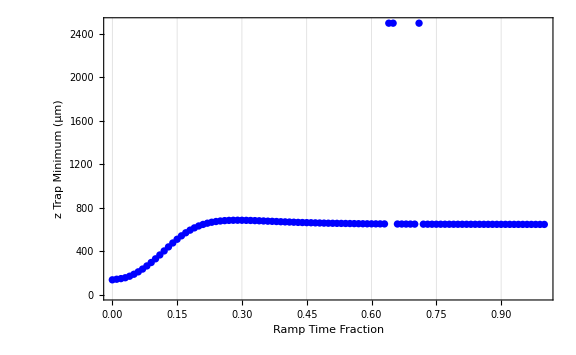
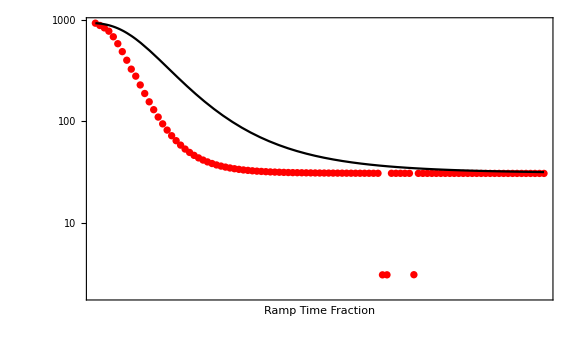

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"z"]
```

{{0.,1.},{1.80409,4.77184}}

{6.07444,118.137}

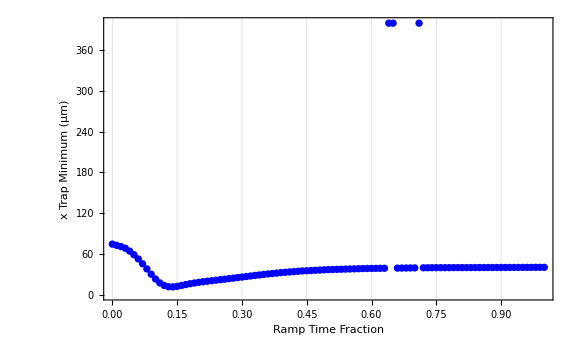
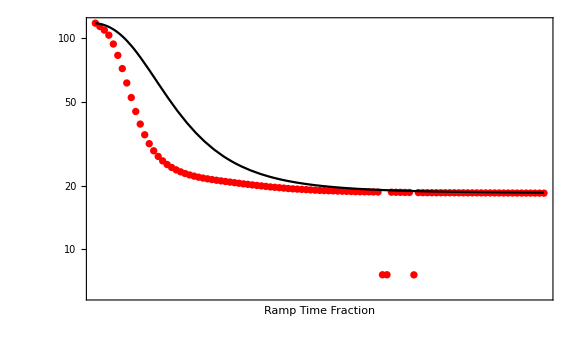

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"x",meanfrequency->False]
```

{{0.,1.},{0.965452,6.87617}}

{2.62598,968.904}

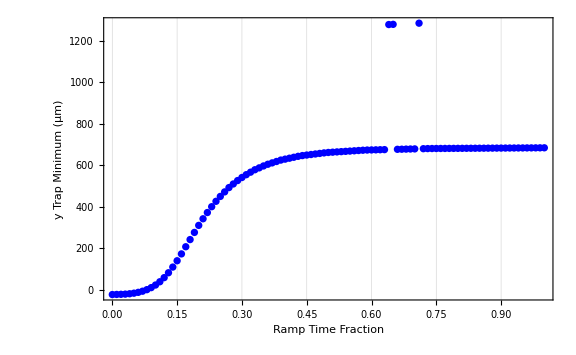
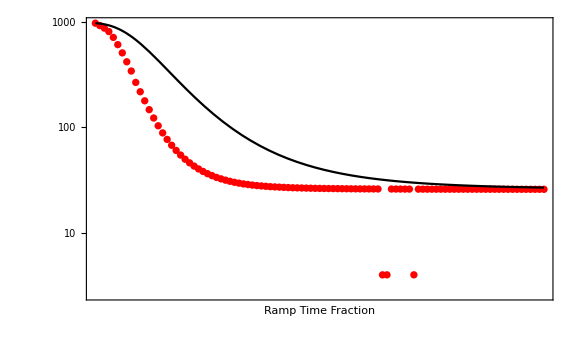

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"y",meanfrequency->False]
```

{{0.,1.},{0.668287,6.83526}}

{1.95089,930.072}

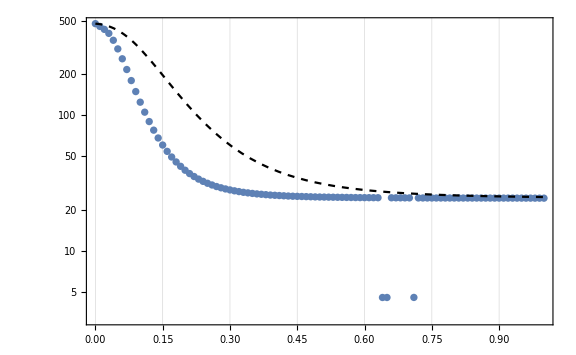

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->False,frequency->False,gridlines->True,usemodel->True,size->Large,axis->"z",meanfrequency->True,meanmodel->True]
```

```mathematica
Beep[]
```

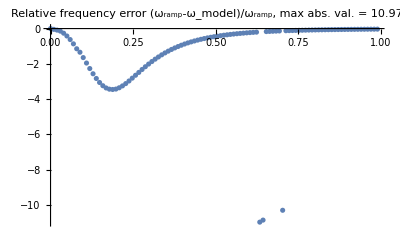

```mathematica
plotFreqError[pts1s]
```

## Export ramp

### Export ramp

```mathematica
trap1short={#⟦1⟧,Table[Total[Take[Round[#⟦2⟧,10.^-5],n]],{n,Length@rampin1s⟦1⟧}]}&[rampin1s]
```

{{0.0272,0.0142,0.0116,0.0102,0.0096,0.009,0.009,0.0088,0.0088,0.0092,0.0046,0.0048,0.0048,0.005,0.005,0.0054,0.0056,0.0058,0.006,0.0064,0.0066,0.0072,0.0076,0.0082,0.0088,0.0096,0.0106,0.0116,0.013,0.0148,0.0166,0.0196,0.0228,0.0278,0.0346,0.0446,0.0606,0.0892,0.1496,0.2656},{0.10797,0.22085,0.32353,0.41194,0.48886,0.55362,0.61134,0.66129,0.70547,0.74579,0.76402,0.78154,0.79793,0.81353,0.82793,0.84213,0.85555,0.86816,0.87986,0.89111,0.90137,0.91137,0.92061,0.92943,0.93753,0.94518,0.95236,0.95904,0.96521,0.97105,0.97621,0.98101,0.98535,0.98913,0.99239,0.9951,0.99714,0.99865,0.99957,1.}}

```mathematica
(* Set the DateStringFormat to help create unique names for each exported beam.The format is inspired by the ISO 8601 standard. *)
generateTimeStamp[]:=DateString[{"Year","Month","Day","T","Hour","Minute","Second"}];
rampTimeStamp=generateTimeStamp[]
```

20210315T190805

```mathematica
Export[FileNameJoin@{outputDirectory,rampTimeStamp<>"_ZHbB3_ramp_40_steps.csv"},trap1shortᵀ]
```

C:\Users\josep\forschung\modeling\bubble_bec\output\20210315T190805_ZHbB3_ramp_40_steps.csv

### Export ramp parameters

```mathematica
exportRampEndpoints[trap1_,trap2_,rampTimeStamp_,outputDirectory_]:=Module[
{
fileName=rampTimeStamp<>"_ramp_endpoints",
table={trap1,trap2},
headings={{"InitialTrap","FinalTrap"},{"IL[A]","IZ[A]","IH[A]","Bx[G]","By[G]","Bz[G]"}}
},
Print[table];
Export[FileNameJoin@{outputDirectory,fileName<>".csv"},table,TableHeadings->headings]
]

exportRampEndpoints[trapzero,trapone,rampTimeStamp,outputDirectory]
```

{{0.,0,0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0.,0,0.,2.425,2.6,-1.95,3.55435,-3.11335}}

C:\Users\josep\forschung\modeling\bubble_bec\output\20210315T190805_ramp_endpoints.csv

```mathematica
Beep[];
Pause[1];
Beep[];
```

## Look at intermediate trap and CAL table values

```mathematica
plotTrapParametersVT[trapzero,trapone,rampin1s,points1s,numberOfSequencePoints,rampDuration->700]
```

plotTrapParametersVT[{0.,0,0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0.,0,0.,2.425,2.6,-1.95,3.55435,-3.11335},{{0.0272,0.0142,0.0116,0.0102,0.0096,0.009,0.009,0.0088,0.0088,0.0092,0.0046,0.0048,0.0048,0.005,0.005,0.0054,0.0056,0.0058,0.006,0.0064,0.0066,0.0072,0.0076,0.0082,0.0088,0.0096,0.0106,0.0116,0.013,0.0148,0.0166,0.0196,0.0228,0.0278,0.0346,0.0446,0.0606,0.0892,0.1496,0.2656},{0.10797,0.11288,0.10268,0.08841,0.07692,0.06476,0.05772,0.04995,0.04418,0.04032,0.01823,0.01752,0.01639,0.0156,0.0144,0.0142,0.01342,0.01261,0.0117,0.01125,0.01026,0.01,0.00924,0.00882,0.0081,0.00765,0.00718,0.00668,0.00617,0.00584,0.00516,0.0048,0.00434,0.00378,0.00326,0.00271,0.00204,0.00151,0.00092,0.00043}},100,40,rampDuration→700]